```mathematica
ClearAll["Global`*"]
```

# Template for Power Spectrum of GW from order PT

```mathematica
gn[tau_,beta_,n_]:=Piecewise[{{(4*beta^2 tau *(1/beta-tau))^(n-1),0<tau<1/beta}},0];
R[v_,beta_]:=v/beta;
Fmodulo[k_,v_,beta_] :=R[v,beta]^3/(1 + (k*R[v,beta])^4);
```

## Coherent scenario

```mathematica
funzioneprova[x_]:=x^2;
xmin = 0;
xmax = 10^3;
deltax = 10^6;
xList = 10^Subdivide[Log10[xmin],Log10[xmax],deltax];
```

```mathematica
dataprovax = Flatten[ParallelTable[{{x},funzioneprova[x]},{x,xList}],1];
interprova = Interpolation[dataprovax,InterpolationOrder->3];
```

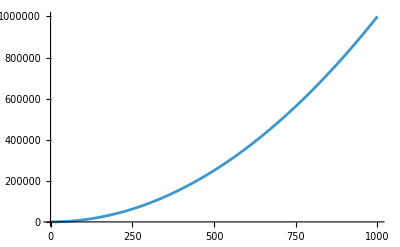

```mathematica
Plot[funzioneprova[x],{x,xmin,xmax}]
```

```mathematica
gFourier[k_?NumericQ,beta_?NumericQ,n_]:=NIntegrate[Abs[gn[tau,beta,n]]*Exp[I*k*tau],{tau,-∞,+∞}];
```

```mathematica
Ps[k_?NumericQ,beta_?NumericQ,v_?NumericQ,n_]:=Fmodulo[k,v,beta]*(Abs[gFourier[k,beta,n]]^2);
```

```mathematica
βkPs[k_?NumericQ,beta_?NumericQ,v_?NumericQ,n_]:=beta^2 * k^3 * Re[Ps[k,beta,v,n]];
```

```mathematica
v1 = 1;
```

```mathematica
kmin = 0;
kmax = 10^5;
dk = 100;
kList = 10^Subdivide[Log10[kmin],Log10[kmax],dk];
```

```mathematica
βmin=0.1;
βmax=10;
dβ=20;
βList = 10^Subdivide[Log10[βmin],Log10[βmax],dβ];
```

```mathematica
data1βkPs = Flatten[ParallelTable[{{k,β},βkPs[k,β,v1,1]},{k,kList},{β,βList}],1];
```

```mathematica
interp1βkPs = Interpolation[data1βkPs,InterpolationOrder->3];
```

Interpolation::indp: There are duplicated abscissa points in {{0.,0.1},{0.,0.125893},{0.,0.158489},{0.,0.199526},{0.,0.251189},{0.,0.316228},{0.,0.398107},{0.,0.501187},{0.,0.630957},{0.,0.794328},{0.,1.},{0.,1.25893},«28»,{0.,7.94328},{0.,10.},{0.,0.1},{0.,0.125893},{0.,0.158489},{0.,0.199526},{0.,0.251189},{0.,0.316228},{0.,0.398107},{0.,0.501187},«2071»}.

```mathematica
Plot3D[interp1βkPs[k,β],{k,kmin,kmax},{β,βmin,βmax}]
```

```mathematica
data2βkPs = Flatten[ParallelTable[{{k,β},βkPs[k,β,v1,2]},{k,kList},{β,βList}],1];
```

```mathematica
interp2βkPs = Interpolation[data2βkPs,InterpolationOrder->3];
```

Interpolation::indp: There are duplicated abscissa points in {{0.,0.1},{0.,0.125893},{0.,0.158489},{0.,0.199526},{0.,0.251189},{0.,0.316228},{0.,0.398107},{0.,0.501187},{0.,0.630957},{0.,0.794328},{0.,1.},{0.,1.25893},«28»,{0.,7.94328},{0.,10.},{0.,0.1},{0.,0.125893},{0.,0.158489},{0.,0.199526},{0.,0.251189},{0.,0.316228},{0.,0.398107},{0.,0.501187},«2071»}.

```mathematica
Plot3D[interp2βkPs[k,β],{k,kmin,kmax},{β,βmin,βmax}]
```

```mathematica
data3βkPs = Flatten[ParallelTable[{{k,β},βkPs[k,β,v1,3]},{k,kList},{β,βList}],1];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small. will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {5.37109}. NIntegrate obtained 1.11994×10^-16-2.02339×10^-17 ⅈ and 4.221×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {4.43707}. NIntegrate obtained -5.0492×10^-16-1.70166×10^-15 ⅈ and 3.8022×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.2657}. NIntegrate obtained 9.94542×10^-17+9.68633×10^-17 ⅈ and 3.13189×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {3.05411}. NIntegrate obtained -5.73745×10^-16-3.47355×10^-15 ⅈ and 2.49352×10^-19 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in tau near {tau} = {2.38709}. NIntegrate obtained 1.99231×10^-15-2.61558×10^-15 ⅈ and 3.79052×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate failed to converge to prescribed accuracy after `1` recursive bisections in `2` near `3` = `4`. NIntegrate obtained `5` and `6` for the integral and error estimates. will be suppressed during this calculation.

```mathematica
interp3βkPs = Interpolation[data3βkPs,InterpolationOrder->3];
```

```mathematica
Plot3D[interp3βkPs[k,β],{k,kmin,kmax},{β,βmin,βmax}]
```

## , (we use case ) , ,

```mathematica
(* Given parameter *)
beta=1;
v = 1;
```

```mathematica
g2[tau_]:=Piecewise[{{4*beta^2 tau *(1/beta-tau),0<tau<1/beta}},0];
L[tau_] := v/beta*g2[tau];
f[tau_,k_]:=L[tau]^(3/2)  √((1 + ((k*L[tau])/3)^2)/(1 + ((k*L[tau])/2)^2 +((k*L[tau])/3)^6)) ;
```

## Fourier transform ,

```mathematica
fTdf[q0_?NumericQ,q_?NumericQ]:=NIntegrate[f[tau,q]*Exp[-I*q0*tau],{tau,0,1/beta}];
fstarTdf[q0_?NumericQ,q_?NumericQ]:=NIntegrate[ComplexExpand[f[tau,q]]*Exp[I*q0*tau],{tau,0,1/beta}];
DeltaS[q0_?NumericQ,q_?NumericQ]:=fTdf[q0,q]*fstarTdf[q0,q];
spectrumFixedRatio[q0_?NumericQ,r_?NumericQ]:=q0^3 DeltaS[q0,q0/r];
```

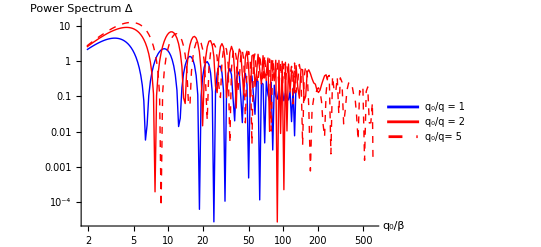

```mathematica
LogLogPlot[{spectrumFixedRatio[q0,1.0],spectrumFixedRatio[q0,2.0],spectrumFixedRatio[q0,5.0]},{q0,0.0,1000.0},AxesLabel->{"q_0/β","Power Spectrum Δ"},PlotLegends->{"q_0/q = 1","q_0/q = 2","q_0/q= 5"},PlotStyle->{Directive[Thick,Blue],Directive[Thick,Red],Directive[Thick,Red,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Varying velocity and PT time scale

```mathematica
ClearAll["Global`*"]
```

```mathematica
g2[tau_,beta_]:=Piecewise[{{4*beta^2 tau *(1/beta-tau),0<tau<1/beta}},0];
L[tau_,beta_,v_] := v/beta*g2[tau,beta];
f[tau_,q_,beta_,v_]:=L[tau,beta,v]*√(v/beta) √((1 + ((q*L[tau,beta,v])/3)^2)/(1 + ((q*L[tau,beta,v])/2)^2 +((q*L[tau,beta,v])/3)^6)) ;
fTdf[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=NIntegrate[f[tau,q,beta,v]*Exp[-I*q0*tau],{tau,0,1/beta}];
fstarTdf[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=NIntegrate[ComplexExpand[f[tau,q,beta,v]]*Exp[I*q0*tau],{tau,0,1/beta}];
DeltaS[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=fTdf[q0,q,beta,v]*fstarTdf[q0,q,beta,v];
spectrum[q0_?NumericQ,r_?NumericQ,beta_?NumericQ,v_?NumericQ]:=q0^3 DeltaS[q0,q0/r,beta,v];
```

## Velocity

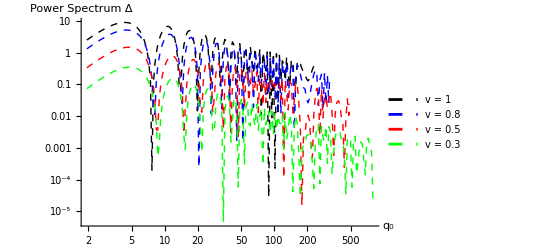

```mathematica
LogLogPlot[{spectrum[q0,2.0,1,1],spectrum[q0,2.0,1,0.8],spectrum[q0,2.0,1,0.5],spectrum[q0,2.0,1,0.3]},{q0,0.0,1000.0},AxesLabel->{"q_0","Power Spectrum Δ"},PlotLegends->{"v = 1","v = 0.8","v = 0.5","v = 0.3"},PlotStyle->{Directive[Thick,Black,Dashed],Directive[Thick,Blue,Dashed],Directive[Thick,Red,Dashed],Directive[Thick,Green,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Inverse time PT

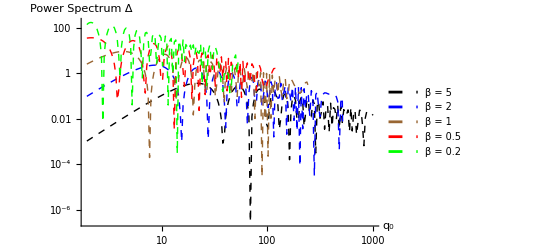

```mathematica
LogLogPlot[{spectrum[q0,2.0,5,1],spectrum[q0,2.0,2,1],spectrum[q0,2.0,1,1],spectrum[q0,2.0,0.5,1],spectrum[q0,2.0,0.2,1]},{q0,0.0,1000.0},AxesLabel->{"q_0","Power Spectrum Δ"},PlotLegends->{"β = 5","β = 2","β = 1","β = 0.5","β = 0.2"},PlotStyle->{Directive[Thick,Black,Dashed],Directive[Thick,Blue,Dashed],Directive[Thick,Brown,Dashed],Directive[Thick,Red,Dashed],Directive[Thick,Green,Dashed]},PlotRange->All,MaxRecursion->2]
```

## Final abundance

```mathematica
G = 1;
h = 0.67;
ρc = (3 *h^2)/(8 π G);
```

```mathematica
fh[q0_,q_]:=((q0^2-q^2)^2)/2;
cJ = 4/3;(* scalar*)
diffΩIntegrand[q0_?NumericQ,q_?NumericQ,beta_?NumericQ,v_?NumericQ]:=fh[q0,q]/q*DeltaS[q0,q,beta,v];
diffΩ[q0_?NumericQ,beta_?NumericQ,v_?NumericQ]:=2 cJ/(320 π^2)*NIntegrate[diffΩIntegrand[q0,q,beta,v],{q,10^-5,q0}];
Ω[beta_?NumericQ,v_?NumericQ]:=NIntegrate[diffΩ[q0,beta,v],{q0,0,2*beta},Method->"GlobalAdaptive"];
```

```mathematica
(* consider ultrarelativistic bubbles *)
βvalues = {0.2,0.5,1,2,5};
Ωvalues = ConstantArray[0,Length[βvalues]];
For[i=1,i<=Length[βvalues],i++,Ωvalues[[i]]=Ω[βvalues[[i]],1]];
```

```mathematica
dataΩβ = Transpose[{βvalues,Ωvalues}];
```

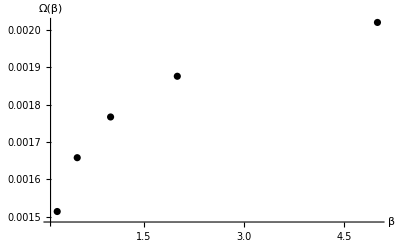

```mathematica
ListPlot[dataΩβ,AxesLabel->{"β","Ω(β)"},PlotStyle->{Directive[Black]},PlotRange->All]
```